## Distance between two 1D subspaces

```mathematica
helper[u_,v_]:=Module[{s},
Quiet[{_,s,_}=SingularValueDecomposition[{{Conjugate[u].v}}]];
Sin[ArcCos[s[[1]]]]
];
```

```mathematica
eigvecDist[m_,t_]:=Module[{u,v,eig,eigvec,i1,i2},
{eig,eigvec}=Eigensystem[N[Transpose[m]]];
i1=Ordering[Abs[eig-t],1][[1]];
i2=Ordering[Abs[eig-eig[[i1]]],2][[2]];
u=eigvec[[i1]];
v=eigvec[[i2]];
helper[u,v]
];
eigvalDist[m_,t_]:=Module[{eig,i1,i2},
eig=Eigenvalues[N[Transpose[m]]];
i1=Ordering[Abs[eig-t],1][[1]];
i2=Ordering[Abs[eig-eig[[i1]]],2][[2]];
Abs[eig[[i1]]-eig[[i2]]]
];
```

## Example

```mathematica
s[p_]:={{0,1,0,0,0},{0,0,1-p,p,0},{1,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0}};
```

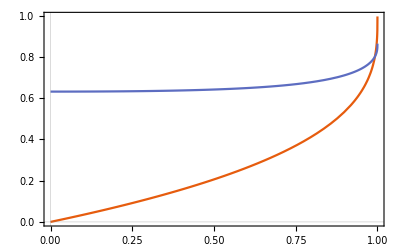

```mathematica
Plot[{eigvalDist[s[p],1],eigvecDist[s[p],1]},{p,0,1},PlotTheme->"Scientific"]
```

```mathematica
Eigensystem[N[Transpose[s[0.992]]]]
```

{{-1.,1.,-0.1+0.173205 ⅈ,-0.1-0.173205 ⅈ,0.2},{{-1.17425×10^-17+0. ⅈ,-1.06627×10^-16+0. ⅈ,-7.09413×10^-18+0. ⅈ,-0.707107+0. ⅈ,0.707107+0. ⅈ},{1.57516×10^-17+0. ⅈ,-1.3519×10^-17+0. ⅈ,1.17169×10^-17+0. ⅈ,0.707107+0. ⅈ,0.707107+0. ⅈ},{-0.0702875+0.121742 ⅈ,0.702875+0. ⅈ,-0.0140575-0.0243483 ⅈ,0.0642629-0.120582 ⅈ,-0.682793+0.0231889 ⅈ},{-0.0702875-0.121742 ⅈ,0.702875+0. ⅈ,-0.0140575+0.0243483 ⅈ,0.0642629+0.120582 ⅈ,-0.682793-0.0231889 ⅈ},{-0.136333+0. ⅈ,-0.681663+0. ⅈ,-0.0272665+0. ⅈ,0.140877+0. ⅈ,0.704385+0. ⅈ}}}

```mathematica
Eigensystem[N[Transpose[s[0.00000001]]]]
```

{{1.,-1.,-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ,1.},{{1.68102×10^-8+0. ⅈ,1.68102×10^-8+0. ⅈ,1.68102×10^-8+0. ⅈ,-0.707107+0. ⅈ,-0.707107+0. ⅈ},{2.99436×10^-17+0. ⅈ,-2.34297×10^-17+0. ⅈ,2.91407×10^-17+0. ⅈ,0.707107+0. ⅈ,-0.707107+0. ⅈ},{-0.288675+0.5 ⅈ,0.57735+0. ⅈ,-0.288675-0.5 ⅈ,8.01876×10^-18-3.33333×10^-9 ⅈ,-2.88675×10^-9+1.66667×10^-9 ⅈ},{-0.288675-0.5 ⅈ,0.57735+0. ⅈ,-0.288675+0.5 ⅈ,8.01876×10^-18+3.33333×10^-9 ⅈ,-2.88675×10^-9-1.66667×10^-9 ⅈ},{0.365148+0. ⅈ,0.365148+0. ⅈ,0.365148+0. ⅈ,-0.547723+0. ⅈ,-0.547723+0. ⅈ}}}

```mathematica
Abs[eigvalDist[s[0.5],1]-eigvecDist[s[0.5],1]]
```

{0.436279}

## Disjoint Boxing Network

```mathematica
s1={{0,1,0,0,0},{0,0,1,0,0},{1,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0}};
s2={{0,1,0,0,0},{0,0,1/2,1/2,0},{1,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0}};
s3={{0,1,0,0,0},{0,0,1-10*$MachineEpsilon,10*$MachineEpsilon,0},{1,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0}};
```

```mathematica
{e1,v1}=Eigensystem[N[Transpose[s1]]]
{e2,v2}=Eigensystem[N[Transpose[s2]]]
{e3,v3}=Eigensystem[N[Transpose[s3]]]
```

{{-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ,-1.,1.,1.},{{0.57735+0. ⅈ,-0.288675-0.5 ⅈ,-0.288675+0.5 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.57735+0. ⅈ,-0.288675+0.5 ⅈ,-0.288675-0.5 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.707107+0. ⅈ,0.707107+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.707107+0. ⅈ,0.707107+0. ⅈ},{-0.57735+0. ⅈ,-0.57735+0. ⅈ,-0.57735+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}}

{{1.,-1.,0.793701,-0.39685+0.687365 ⅈ,-0.39685-0.687365 ⅈ},{{6.02422×10^-16+0. ⅈ,8.12255×10^-17+0. ⅈ,5.68578×10^-16+0. ⅈ,-0.707107+0. ⅈ,-0.707107+0. ⅈ},{-3.88896×10^-16+0. ⅈ,-7.97129×10^-17+0. ⅈ,2.94153×10^-16+0. ⅈ,-0.707107+0. ⅈ,0.707107+0. ⅈ},{-0.354857+0. ⅈ,-0.447092+0. ⅈ,-0.28165+0. ⅈ,0.479485+0. ⅈ,0.604113+0. ⅈ},{0.265878-0.460514 ⅈ,-0.669971+0. ⅈ,0.211028+0.365511 ⅈ,-0.024271+0.185173 ⅈ,0.217336-0.0901689 ⅈ},{0.265878+0.460514 ⅈ,-0.669971+0. ⅈ,0.211028-0.365511 ⅈ,-0.024271-0.185173 ⅈ,0.217336+0.0901689 ⅈ}}}

{{1.,-1.,1.,-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ},{{0.167578+0. ⅈ,0.167578+0. ⅈ,0.167578+0. ⅈ,0.676665+0. ⅈ,0.676665+0. ⅈ},{4.75276×10^-17+0. ⅈ,5.15194×10^-17+0. ⅈ,3.97309×10^-17+0. ⅈ,-0.707107+0. ⅈ,0.707107+0. ⅈ},{-0.319536+0. ⅈ,-0.319536+0. ⅈ,-0.319536+0. ⅈ,0.588936+0. ⅈ,0.588936+0. ⅈ},{-0.288675+0.5 ⅈ,0.57735+0. ⅈ,-0.288675-0.5 ⅈ,6.67823×10^-31-7.40149×10^-16 ⅈ,-6.40988×10^-16+3.70074×10^-16 ⅈ},{-0.288675-0.5 ⅈ,0.57735+0. ⅈ,-0.288675+0.5 ⅈ,6.67823×10^-31+7.40149×10^-16 ⅈ,-6.40988×10^-16-3.70074×10^-16 ⅈ}}}

```mathematica
v1[[4]]
v1[[5]]
dist[v1[[4]],v1[[5]]]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.707107+0. ⅈ,0.707107+0. ⅈ}

{-0.57735+0. ⅈ,-0.57735+0. ⅈ,-0.57735+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{1.}

```mathematica
v2[[1]]
v2[[3]]
dist[v2[[1]],v2[[3]]]
```

{6.02422×10^-16+0. ⅈ,8.12255×10^-17+0. ⅈ,5.68578×10^-16+0. ⅈ,-0.707107+0. ⅈ,-0.707107+0. ⅈ}

{-0.354857+0. ⅈ,-0.447092+0. ⅈ,-0.28165+0. ⅈ,0.479485+0. ⅈ,0.604113+0. ⅈ}

{0.642579}

```mathematica
v3[[1]]
v3[[3]]
dist[v3[[1]],v3[[3]]]
```

{0.167578+0. ⅈ,0.167578+0. ⅈ,0.167578+0. ⅈ,0.676665+0. ⅈ,0.676665+0. ⅈ}

{-0.319536+0. ⅈ,-0.319536+0. ⅈ,-0.319536+0. ⅈ,0.588936+0. ⅈ,0.588936+0. ⅈ}

{0.771373}

```mathematica
Abs[e3[[1]]-e3[[3]]]/Abs[e3[[1]]]
```

1.11022×10^-15